```mathematica
α=(3+n)/Log[2+n]*Log[(3+n)/2]
```

((3+n) Log[(3+n)/2])/Log[2+n]

```mathematica
Manipulate[Plot[1-1 / x^(n+1) * 1/(1+(L/x)^(((3+n) Log[(3+n)/2])/Log[2+n]))^((3+n)/(((3+n) Log[(3+n)/2])/Log[2+n])), {x,0,10}],{n,0,6},{L,0.1,10}]
```

```mathematica
D[A/x^(n+1) *h[x], x]
```

A (-1-n) x^(-2-n) h[x]+A x^(-1-n) h'[x]

```mathematica
h[x_]=1/(1+(L/x)^a)^((3+n)/a)
```

(1+(L/x)^a)^(-(3+n)/a)

```mathematica
D[h[x],x]/h[x] // FullSimplify
```

((3+n) (L/x)^a)/((1+(L/x)^a) x)

```mathematica
(* ACHTUNG: Ich bin der Meinung, dass folgender Plot falsch ist, auch wenn er gut aussieht. Es ist -Subscript[T, H], da wuerde also mindestens mal ein minus fehlen. *)
```

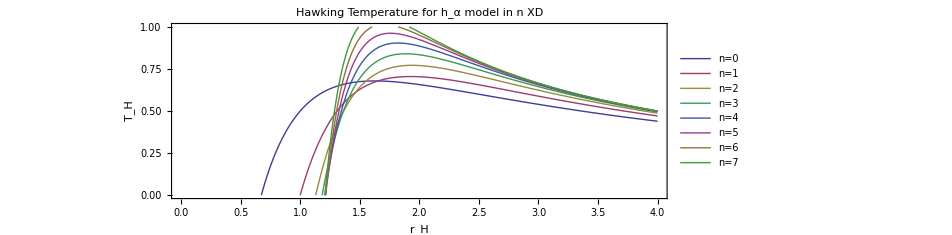

```mathematica
Plot[Evaluate[Table[-1/x((n+1)-(3+n)*x^(((3+n) Log[(3+n)/2])/Log[2+n])/(1+x^(((3+n) Log[(3+n)/2])/Log[2+n]))),{n,0,7}]],  {x,0,4},PlotRange-> {0,1},
PlotLegends->Placed[Table["n="<>ToString[n],{n,0,7}],{Left,Bottom}],Frame->True,FrameLabel->{Subscript[r, H],"T_H"},
AspectRatio->1/3,
PlotLabel->"Hawking Temperature for h_α model in n XD"]
```

```mathematica
Table[(1+n)^(((3+n) Log[(3+n)/2])/Log[2+n])*(-(n+1)+(n+3)*1/(1+(1/(1+n)))) // FullSimplify//N, {n,0,7}]
```

{0.5,3.83375,28.3049,233.835,2196.65,23333.6,277591.,3.66321×10^6}

```mathematica
(* Bei diesen r-Werten wird T_H = 0. Das ist nicht gut!! *)
```

```mathematica
Solve[1/x(-(n+1)+(3+n)*x^a/(1+x^a))==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2^(-1/a) (1+n)^(1/a)}}

```mathematica
Style[\[FreakedSmiley],FontSize-> 88](* FreakedSmiley = wolfram 404 icon *)
```

\[FreakedSmiley]